# Data Science and Machine Learning

## Personal Assignment 1: Manipulating, cleaning, visualizing data

In this assignment, we will use a dataset to perform cleaning and visualization operations.
We will first use clean data from company entities.
Then, we will use a dataset about the performance of several companies across different years. The performance is shown in terms of different social, environmental, and governance scores. For each company, the dataset also contains a set of features, e.g, market value, assets, etc.
Once you are done you have to:
       1. Submit your notebook here: https://moodle.epfl.ch/mod/assign/view.php?id=1159929
       2. Answer the questions to the quiz: https://moodle.epfl.ch/mod/quiz/view.php?id=1171854
You have to do both. The answers to the quiz should be supported by your code. If they are not you will not receive the point for it. 

If there is need for further clarifications on the questions, post your questions in the #assignments of our slack channel.  Anyone can answer without divulging the solution. If needed, after the assignment is released, we will update this file, so make sure you check the git repository for updates.

Note: This assignment is strictly personal, so do as much as you can on your own. Sharing/collaboration is only supported for the project!

Good luck!

## Warm-Up (..the clean data...)

For the companies: {"Zoom Video Communications","Apple","Biogen","Amazon","Adobe","Invesco Ltd","Facebook","Microsoft"}, create a data structure containing their "CurrentAssets".
Your structure should be an association with keys being company entities.

```mathematica
companies = {"Zoom Video Communications", "Apple", "Biogen", "Amazon",
   "Adobe", "Invesco Ltd", "Facebook", "Microsoft"};
companyEntities = Interpreter["Company"][#] & /@ companies
```

{Zoom Video Communications,Apple,Biogen,Amazon.com,Adobe,Invesco,Facebook,Microsoft}

```mathematica
companiesAsset =EntityValue[companyEntities, "CurrentAssets", "EntityAssociation"]
```

<|Zoom Video Communications→3.74753×10^9 $,Apple→1.3342675×10^11 $,Biogen→7.15835×10^9 $,Amazon.com→1.195045×10^11 $,Adobe→7.74875×10^9 $,Invesco→3.64958×10^9 $,Facebook→7.4872×10^10 $,Microsoft→1.752675×10^11 $|>

Question 1: 
What are the current assets of Zoom Video Communications? [1 point]
Give your answer in billion $, rounded at two-digit precision (e.g., 1.23)

```mathematica
assetZoom = Round[companiesAsset[Interpreter["Company"]["Zoom Video Communications"]]/10^9,0.01]
```

3.75 $

Sort this data structure, on decreasing order of their current assets.

```mathematica
sortedCompanies=ReverseSort[companiesAsset]
```

<|Microsoft→1.752675×10^11 $,Apple→1.3342675×10^11 $,Amazon.com→1.195045×10^11 $,Facebook→7.4872×10^10 $,Adobe→7.74875×10^9 $,Biogen→7.15835×10^9 $,Zoom Video Communications→3.74753×10^9 $,Invesco→3.64958×10^9 $|>

Question 2: 
Which is the company with the 2nd highest current assets? [1 point]

```mathematica
Keys[sortedCompanies][[2]]
```

Apple

Make a BarChart to show the sorted list, displaying the current assets in billion $. Annotate the x-axis with the name of the company.

```mathematica
companiesAssetBillion=sortedCompanies/10^9;
```

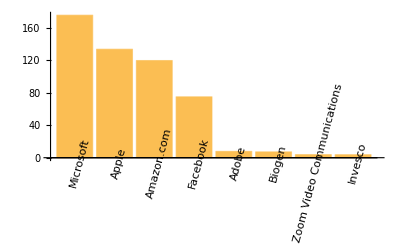

```mathematica
barAssets = BarChart[companiesAssetBillion,
     ChartLabels ->Placed[Keys[sortedCompanies],Below, Rotate[#, Pi/2.4] &]]
```

Make a PieChart of the current assets.  Add a ChartLegends with the company names, and ChartLabels with the share of each company in %.

```mathematica
shareCompanies = Round[#*100/Total[#],0.1]&[companiesAssetBillion];
```

```mathematica
PieChart[companiesAssetBillion, 
ChartStyle -> "DarkRainbow",
ChartLabels -> Placed[Quantity[Values[shareCompanies],"%"],"RadialCallout"],
ChartLegends ->Keys[sortedCompanies]]
```

-Graphics-

Question 3:
What is the share of current assets of Microsoft?  [1 point]

```mathematica
shareCompanies[Entity["Company","MicrosoftCorporation::j3gxm"]]
```

33.36

Plot a GeoBubbleChart where each bubble is a company centered at its longitude/latitude, and the size of the bubble is the current assets of the company.

```mathematica
geoCompanies = GeoBubbleChart[companiesAssetBillion, ChartStyle -> 3]
```

-Graphics-

Question 4:
Where are located the companies with the highest current assets?  [1 point]

## Data acquisition (or dealing with the Dirty-Dirty Data!)

Import the CSV dataset located at this address: https://raw.githubusercontent.com/michalis0/Business-Intelligence-and-Analytics/master/data/ESG_index_companies.csv
Store it in a variable "dataRaw" and do not display the output.
Note: Import it as a dataset, with column keys corresponding to the first row.

```mathematica
dataRaw = Import["https://storage.googleapis.com/mgt_492/ESG_index_companies.csv", "Dataset", "HeaderLines" -> 1];
```

Preview the dataset. Display a RandomSample of 10 rows of your dataset

```mathematica
RandomSample[dataRaw,10]
```

Extract the names of the columns (Keys) to understand what information is displayed in the dataset

```mathematica
dataRaw[Keys][1]
```

Drop the "esg_binaire", "csr_com", "csr_report" columns because they are not reliable.
Store all the remaining data in a variable "dataReliable" and do not display the output.

```mathematica
dataReliable = dataRaw[KeyDrop[{"esg_binaire", "csr_com", "csr_report"}]];
```

Question 5:
How many columns are in the dataset "dataReliable"?  [1 point]

```mathematica
Dimensions[dataReliable]
```

{6582,41}

Question 6:
What is the data type (String, Real, Integer, etc.)  of the first observation of the feature "ESG controversy score"? What about the last observation?  [1 point]
How do you interpret this result?

```mathematica
Head @dataReliable[1,"ESG controversy score" ] 
Head @dataReliable[-1,"ESG controversy score" ]
```

String

Real

The first observation is a missing value:

```mathematica
dataReliable[1,"ESG controversy score" ] ==""
```

True

## Data Cleaning (...or your worst nightmare)

Count the number of missing values in each column. 
Note that there are two types of missing values: "" and "#DIV/0!".
Hints: 
   - One option is to map over a list of the Keys.
   - After counting the number of missing value, you can create an association between a list of keys and a list of missing values to help future operations.

```mathematica
keyList=  dataReliable[Keys][1] //Normal;
```

```mathematica
numMissing = Count[dataReliable[All,#], u_ /;( u==""||u=="#DIV/0!")] & /@ keyList;
```

```mathematica
missAsso = AssociationThread[keyList -> numMissing]
```

<|Year→0,Firm→0,ESG controversy score→961,Environment controversy score→2565,Social controvery score→3389,Governance controversy score→965,Score - Emission Reduction/Biodiversity Controversies (Inactive)→965,Score - Emission Reduction/Spill/Pollution Controversies (Inactive)→2565,Score - Product Innovation/Product Impact Controversies (Inactive)→965,Score - Resource Reduction/Environment Impact Controversy (Inactive)→965,Score - Client Loyalty/Anti-competition Controversy (Inactive)→965,Score - Community/Bribery Corruption Fraud Controversies (Inactive)→965,Score - Community/Critical Countries-Indigenous Controversy (Inactive)→965,Score - Community/Public Health Controversies (Inactive)→965,Score - Diversity and Opportunity/Diversity Controversies (Inactive)→965,Score - Employment Quality/Wages Work Condition Controversy (Inactive)→965,Score - Health & Safety/Health & Safety Controversies (Inactive)→965,Score - Human Rights/Child Labor Controversies (Inactive)→965,Score - Human Rights/Freedom of Association Controversies (Inactive)→965,Score - Human Rights/Human Rights Controversies (Inactive)→965,Score - Product Responsibility/Customer Controversies (Inactive)→965,Score - Product Responsibility/Responsible Mrktg Controversy(Inactive)→3389,Score - Product Responsibility/Social Exclusion Controversy (Inactive)→965,Score - Compensation Policy/Compensation Controversies (Inactive)→965,Score - Shareholder Loyalty/Accounting Controversies (Inactive)→965,Score - Shareholder Loyalty/Insider Dealings Controversies (Inactive)→965,Score - Shareholder Rights/Shareholder Controversies (Inactive)→965,mv→335,mc→250,tobin→359,roe→259,oia→64,ois→90,esg_score→961,assets→59,roa→169,sg→260,lev→111,div→335,ind→0,country→0|>

Question 7:
What is the number of missing values in the column "Social controvery score"?  [1 point]

```mathematica
numMissingSocial = missAsso[[ "Social controvery score"]]
```

3389

Find the four columns with the most missing values and drop them.
Store the new dataset in a variable "dataCleanCol" and do not display it.
Hint: You should expect to drop the following columns: "Environment controversy score", "Social controvery score", "Score - Emission Reduction/Spill/Pollution Controversies (Inactive)", "Score - Product Responsibility/Responsible Mrktg Controversy(Inactive)"

```mathematica
listMostMissing = Keys @TakeLargest[missAsso,4]
```

{Social controvery score,Score - Product Responsibility/Responsible Mrktg Controversy(Inactive),Score - Emission Reduction/Spill/Pollution Controversies (Inactive),Environment controversy score}

```mathematica
dataCleanCol = dataReliable[KeyDrop[listMostMissing]];
```

Delete all the rows that have at least one missing value.
Store the new dataset in a variable "dataClean" and do not display it.
Hint: One option is to use Select and FreeQ

```mathematica
dataClean = dataCleanCol[Select[FreeQ["" | "#DIV/0!"]]];
```

Question 8:
How many rows does the dataset have after dropping those rows?  [1 point]

```mathematica
Dimensions[dataClean]
```

{5196,37}

Question 9:
As you may have noted, for each company we have data for multiple years. For which year do we have more data points lefts? How many companies are in this year?  [1 point]

```mathematica
yearCompaniesMaxData = TakeLargest[dataClean[Counts,"Year"],1]
```

From now on, we will use the subset of the dataset containing the companies data only for the year with the most number of observations:
- Keep only the data for the year with the most number of observations. 
- Store this dataset in a variable "data".
- Check the dimensions of your new dataset and generate a RandomSample of 10 observations.
- Clear the variables you are not using anymore

```mathematica
data = dataClean[Select[#Year == yearCompaniesMaxData[Keys][1] &]];
```

```mathematica
Dimensions[data]
RandomSample[data,10]
```

{1007,37}

## Data Visualization

If you could not perform the previous operations, you can answer the following questions by importing the CSV dataset "data-esg.csv" that is available in Git. Store it in a variable "data" and do not display the output. Import it as a dataset, with column keys corresponding to the first row.

Plot a BoxWhiskerChart of the values in the following columns "ESG controversy score", "Governance controversy score", "esg_score"

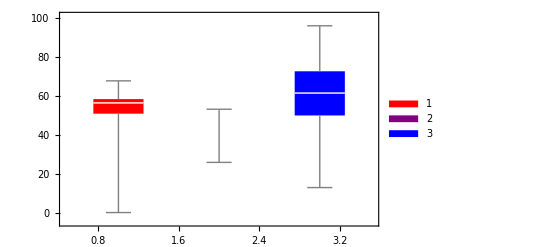

```mathematica
BoxWhiskerChart[{Normal@data[All,"ESG controversy score"],Normal@data[All,"Governance controversy score"],Normal@data[All,"esg_score"]}, ChartLegends ->{"ESG controversy score","Governance controversy score","esg_score"}, ChartStyle ->{Red,Purple, Blue}]
```

Question 10:
Which between the "ESG controversy score", "Governance controversy score", "esg_score" columns has the highest median value?  [1 point]

```mathematica
data[Median, {"ESG controversy score","Governance controversy score","esg_score"}]
```

Normalize all the columns to have values between 0 and 1, except the following ones: "Year", "Firm", "ind", "country".
Store this dataset in a variable "dataN" and do not display the result.

```mathematica
keyListString = {"Year","Firm","ind","country"};
keyListN = Normal @ data[KeyDrop[{"Year","Firm","ind","country"}]][Keys][1];
```

```mathematica
dataN =  Join[data[All,keyListString ],data[Normalize,keyListN],2];
```

Question 11:
What is the normalized value for the "ESG controversy score" for the firm "1&1 DRILLISCH" for the year 2017? (round to 2 decimals, e.g., 0.50)  [1 point]

```mathematica
esgDRILLISCH = Round[dataN[Select[#Firm == "1&1 DRILLISCH" &], "ESG controversy score" ][1],0.01]
```

0.04

Compute the correlation matrix for the following score columns:
"ESG controversy score", 
"Governance controversy score",
"Score - Emission Reduction/Biodiversity Controversies (Inactive)", 
"Score - Community/Critical Countries-Indigenous Controversy (Inactive)",
"Score - Community/Public Health Controversies (Inactive)",
"Score - Diversity and Opportunity/Diversity Controversies (Inactive)"

```mathematica
keyListCorr = {"ESG controversy score", "Governance controversy score",
"Score - Emission Reduction/Biodiversity Controversies (Inactive)", 
"Score - Community/Critical Countries-Indigenous Controversy (Inactive)",
"Score - Community/Public Health Controversies (Inactive)",
"Score - Diversity and Opportunity/Diversity Controversies (Inactive)"};
```

```mathematica
corrMatrix=Correlation[Normal @data[All,keyListCorr][Values]];
```

```mathematica
corrMat =Dataset[AssociationThread[keyListCorr->(AssociationThread[keyListCorr->#]&/@corrMatrix)]]
```

```mathematica
MatrixForm[corrMatrix]
```

(1. | 0.258065 | 0.132304 | 0.00738633 | 0.0700163 | 0.137218
0.258065 | 1. | 0.0515519 | -0.00822108 | 0.380091 | 0.184186
0.132304 | 0.0515519 | 1. | -0.00598213 | -0.00292189 | -0.00594753
0.00738633 | -0.00822108 | -0.00598213 | 1. | -0.0018903 | -0.00391373
0.0700163 | 0.380091 | -0.00292189 | -0.0018903 | 1. | 0.499367
0.137218 | 0.184186 | -0.00594753 | -0.00391373 | 0.499367 | 1.)

Question 12:
What is the correlation between the columns "ESG controversy score" and "Governance controversy score"? (round to 2 decimals, e.g., 0.50)  [1 point]

```mathematica
Round[corrMat["ESG controversy score","Governance controversy score"],0.01]
```

0.26

Generate a MatrixPlot of the correlation matrix

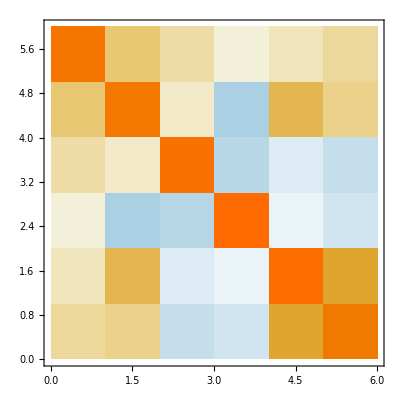

```mathematica
MatrixPlot[corrMatrix]
```

Plot a histogram of the "assets" column (non-normalized) in order to get an idea of the distribution of the amount of assets belonging to the companies in this dataset. To make the histogram more readable use a logarithmic scale on the y-axis (x-axis are the bins of asset values).

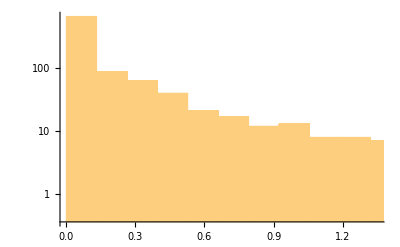

```mathematica
Histogram[data[All,"assets"],ScalingFunctions ->{None,"Log"}]
```

Question 13:
What does the shape of the assets values histogram (in log scale) look like (from left to right, from smaller to larger values)? Decreasing, increasing, almost uniform, very irregular?  [1 point]

For each country, compute the number of companies and the average amount of market value ("mv" column) for the companies in the country.

```mathematica
countryLis = Normal @DeleteDuplicates @ data[All,"country"];
```

```mathematica
companyCountry =Normal @ CountsBy[data,"country"][Values];
```

```mathematica
mvMeanCountry =GroupBy[data,"country"][#][Mean,"mv"] &/@ countryLis;
```

```mathematica
dataCountry = Transpose @ Dataset @ AssociationThread[{"country","count","average_mv"} ->{countryLis,companyCountry, mvMeanCountry}]
```

Question 14:
How many companies are in country "GB"?  [1 point]
Hint: the number should be between 300-400

```mathematica
dataCountry[Select[#country=="GB"&],"count"]
```